```mathematica
(* Returns a Nested list of pair of points representing each line in polygon*)
lineList[list_]:=Partition[Append[list,First[list]],2,1]
```

```mathematica
(*Returns a Normal Vector for a line between two points*)
normalVector[{{x2_,y2_},{x1_,y1_}}]:=Normalize[{(-y2+y1),x2-x1} ]
```

```mathematica
(*Returns a Vector for a line between two points*)
vector[{{x2_,y2_},{x1_,y1_}}]:={x2-x1,y2-y1}
```

```mathematica
findConvexHullCoordsConvexPolysAS[polyRobot_,polyObstacle_]:=Module[{pts},
(* this function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Jan 2, 2019*)
(*First, place the robot at each vertix of the obstacle, and record the vertices coordinates, then flatten this list*)
pts =Flatten[ Table[polyObstacle⟦i⟧- polyRobot⟦j⟧,{i,1,Length[polyObstacle]},{j,1,Length[polyRobot]}],1];
(*second, grab an ordered list of convex hull of these points*)#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[pts]
]
```

```mathematica
(*Returns the Area of a Polygon*)
(*Reference :- https://www.seas.upenn.edu/~sys502/extra_materials/Polygon%20Area%20and%20Centroid.pdf *)
areaCalulation[{{x1_,y1_},{x2_,y2_}}]:=(x1 *y2)-(x2*y1)
areaOfPoly[poly_]:=1/2 *Total@((areaCalulation@#)&/@lineList@poly)
```

```mathematica
(*Returns the centroid of a Polygon*)
(*Reference :- https://www.seas.upenn.edu/~sys502/extra_materials/Polygon%20Area%20and%20Centroid.pdf *)
centroidCal[{{x1_,y1_},{x2_,y2_}}]:={(x1 +x2)*((x1*y2) - (x2*y1)),(y1 +y2)*((x1*y2) - (x2*y1))}
centroidOfPoly[poly_]:=Module[{area=areaOfPoly@poly},If[area≠ 0,(Total@((centroidCal@#)&/@lineList@poly))/(6*area) , Mean@poly]]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ConvexMinkowskiSumRev3[robot_,obstacle_]:=Module[{rl=Length@robot,ol=Length@obstacle,pattern={0,1},rc=centroidOfPoly@robot,robotVectors,obstacleVectors,sortedVectors,pos,ov = 1,rv=0,prev},
robotVectors = {If[rl≥2,-normalVector[#]],If[rl≥2,-vector[#]],rv,#}&/@(lineList@robot);
obstacleVectors={If[ol≥2,normalVector[#]],If[ol≥2,vector[#]],ov,#}&/@(lineList@obstacle);
sortedVectors =Sort[{If[(#⟦1⟧≠ {0,0}) ,N@(ArcTan@@#⟦1⟧)],#⟦2⟧,#⟦3⟧,#⟦4⟧}&/@Join [robotVectors,obstacleVectors],#1⟦1⟧<#2⟦1⟧&];
pos=SequencePosition[sortedVectors⟦;;,3⟧,pattern]⟦1,1⟧;
prev=rc+sortedVectors⟦pos+1⟧⟦4⟧⟦1⟧-sortedVectors⟦pos⟧⟦4⟧⟦1⟧;
DeleteDuplicates@((Chop[prev=prev-#⟦2⟧])&/@RotateLeft[sortedVectors,pos-1])]
```

0.000650009

-0.00114683

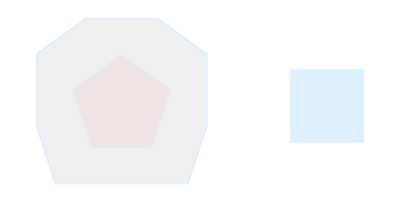

```mathematica
robot =({2,0}+#)&/@ CirclePoints[4];
obstacle =({-2,0}+#)&/@ CirclePoints[5];
ol=Length@obstacle;
oc=If[ol≥3,centroidOfPoly@obstacle,Mean@robot];
(*rl=Length@robot;
ol=Length@obstacle;
pattern={"α","β"};
rc=If[rl≥3,centroidOfPoly@robot,Mean@robot];
robotVectors = {If[rl≥2,-normalVector[#]],If[rl≥2,-vector[#]],"α",#}&/@(lineList@robot);
obstacleVectors={If[ol≥2,normalVector[#]],If[ol≥2,vector[#]],"β",#}&/@(lineList@obstacle);
sortedVectors =Sort[N@{If[#⟦1⟧≠{0,0} ,ArcTan@@#⟦1⟧],#⟦2⟧,#⟦3⟧,#⟦4⟧}&/@Join [robotVectors,obstacleVectors],#1⟦1⟧<#2⟦1⟧&];
pos=SequencePosition[sortedVectors⟦;;,3⟧,pattern]⟦1,1⟧;
prev=rc+sortedVectors⟦pos+1⟧⟦4⟧⟦1⟧-sortedVectors⟦pos⟧⟦4⟧⟦1⟧;
minkowskiPoints=DeleteDuplicates@((Chop[prev=prev-#⟦2⟧])&/@RotateLeft[sortedVectors,pos-1]);
*)
t1=AbsoluteTiming[ConvexMinkowskiSumRev3[robot,obstacle]];
t2=AbsoluteTiming[(-oc+#)&/@findConvexHullCoordsConvexPolysAS[robot,obstacle]];
t3=AbsoluteTiming[mink[robot,obstacle]];
t1⟦1⟧-t2⟦1⟧
t3⟦1⟧-t2⟦1⟧
t3⟦1⟧-t2⟦1⟧
Graphics[{{EdgeForm[Thin],LightBlue,Polygon@robot,LightRed,Polygon@obstacle,LightGreen,Opacity[0.5],Polygon@c1,LightPurple,Opacity[0.5],Polygon@c2}}]
```

```mathematica
(*robot1 =({2,0}+#)&/@ CirclePoints[4];
obstacle1 =({-2,0}+#)&/@ CirclePoints[5];
rc= Mean@robot1;
poly=Flatten[Table[((rc+obstacle1⟦j⟧-#)&/@robot1),{j,1,Length@obstacle1}],1];
mink=#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[poly];
Graphics[{{EdgeForm[Thin],LightBlue,Polygon@robot,LightRed,Polygon@obstacle},{EdgeForm[Thin],LightGreen,Opacity[0.5],Polygon@mink}}]*)
```

```mathematica
mink[robot_,obstacle_]:=Module[{rc=centroidOfPoly@robot,ol=Length@obstacle,pts},
pts=Flatten[Table[((rc+obstacle⟦j⟧-#)&/@robot),{j,1,ol}],1];
#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[pts];
]
```